# Conjugate Gradients and Related Algorithms

An indexed set of vectors p_i is orthogonal if p_i.p_j=0 when i!=j.  The set is orthonormal if
	p_i.p_j=δ_ij=Piecewise[{{1, if i=j}, {0, if i≠j}}]

A square matrix Q is orthogonal if Qᵀ=Q^-1.  
	Q=[p_1|p_2|…|p_m]
is orthogonal iff the set of vectors p_(1:m)⊂ℝ^m are orthonormal.

A tall skinny (TS) m×n matrix Q is orthogonal if Qᵀ.Q=I_n is orthogonal iff the set of vectors p_(1:n)⊂ℝ^m are orthonormal.

An indexed set of vectors p_i are conjugate with respect to a matrix A if for i≠j
	p_i.A.p_j=0.

Two sets of indexed vectors p_i and  (p̂)_i are bi-conjugate with respect to a matrix A if for i≠j
	(p̂)_i.A.p_j=0.

A pair λ_i and v_i≠0 satisfying 
	A.v_i=λ_i v_i
is an eigenpair of a square matrix A.

Almost all square matrices have a full set of linearly independent (LI) eigenvectors. 
Unusual matrices that do not have a full set are  “defective”.  
Matrices that have a full set of LI eigenvectors are “diagonalizable” or sometimes “semi-simple”.

The eigen decomposition of a matrix A is 
	A=V.Λ.V^-1
where V=[v_1|v_2|…|v_m] is the matrix with columns of eigenvectors and Λ=diag(λ_1,λ_2,…,λ_m) is the diagonal matrix formed from the eigenvalues.

A real symmetric matrix S has an orthogonal set of eigenvectors with real eigenvalues.  We write the eigen decomposition of S as written 
	S=Q.Λ.Q^ᵀ
to remind us that the matrix of eigenvectors Q=[v_1|v_2|…|v_m] is orthogonal i.e. Qᵀ=Q^-1

If A is symmetric and positive definite (SPD) then A=Q.Λ.Qᵀ and the unique SPD square root is
	√A=Q.√Λ.Qᵀ.
where √Λ=diag(√λ_1,√λ_2,…,√λ_m) is the diagonal matrix formed from the positive square roots of the eigenvalues.

If A is symmetric and positive definite (SPD) then it defines the alternative inner product
	⟨x,y⟩_A:=⟨x,A.y⟩ = ⟨A.x,y⟩ =⟨√A.x,√A.y⟩ 
If A is not SPD then x.A.y is not an inner product.

## Conjugate Directions: What are they good for?

A set of m conjugate directions p_(1:m) in ℝ^m form a basis for ℝ^m.  So the solution x of A.x=b can be written 
	x=∑_(j=1)^m α_j p_j.
Multiply by A and plug into A.x=b to get
	∑_(j=1)^m α_j A.p_j=b
and the take the inner product with p_i to get
	∑_(j=1)^m α_j p_i.A.p_j=p_i.b.
The conjugate direction condition p_i.A.p_j=0 if i≠j eliminates the sum giving
	 ∑_(j=1)^m α_j p_i.A.p_j=α_i p_i.A.p_i=p_i.b
and finally the simple recipe for the coefficients
	α_i=(p_i.b)/(p_i.A.p_i).

## Bi-Conjugate Directions: What are they good for?

If two sets of m LI vectors p_(1:m) and (p̂)_(1:m) in ℝ^m are bi-conjugate then solution x of A.x=b can be written 
	x=∑_(j=1)^m α_j p_j.
Multiply by A and plug into A.x=b to get
	∑_(j=1)^m α_j A.p_j=b
and the take the inner product with (p̂)_i to get
	∑_(j=1)^m α_j(p̂)_i.A.p_j=(p̂)_i.b.
The bi-conjugate direction condition (p̂)_i.A.p_j=0 if i≠j eliminates the sum giving
	 ∑_(j=1)^m α_j(p̂)_i.A.p_j=α_i(p̂)_i.A.p_i=(p̂)_i.b
and finally the simple recipe for the coefficients
	α_i=((p̂)_i.b)/((p̂)_i.A.p_i).

## “Good” Conjugate Directions for A.x=b

With a given set of conjugate directions p_(1:m) the solution is 
	x=∑_(j=1)^m α_j p_j
We are hoping that a partial sum 
	x_k=∑_(j=1)^k α_j p_j
is a good approximation in the sense that 
	||x-x_k||=||∑_(j=k+1)^m α_j p_j||
gets small rapidly as k increases. It would be good if the coefficients 
	α_j=(p_j.b)/(p_j.A.p_j)
got small rapidly.  You can make α_1 as big as possible by choosing p_1 aligned with the right had side b.

## Computing Orthogonal Directions “on the fly” via Arnoldi

You can compute orthogonal directions with the Gram-Schmidt like Arnoldi process
	y=A.q_i
	z=y-∑_(j=1)^i (y.q_j)q_j
	q_(i+1)=z/||z|| 
initialized with any unit vector q_1.  If solving A.x=b it is common to choose q_1=b/||b||. Generating the new direction by multiplying by A generates vectors aligned with “large” eigenvectors of A early in the process.  The Arnoldi is easy to code.

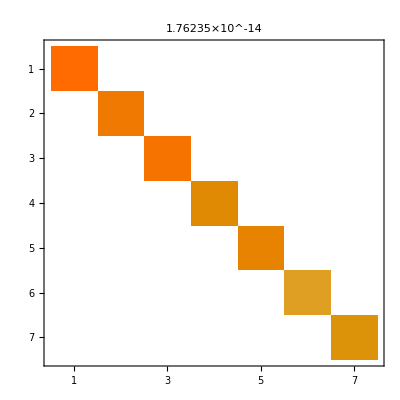

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];
Q=ConstantArray[0,{m,m}];
Q⟦All,1⟧=Normalize[RandomReal[{-1,1},m]];
Do[
y=A.Q⟦All,i⟧;
z=y-Sum[y.Q⟦All,j⟧ Q⟦All,j⟧,{j,1,i}];
Q⟦All,i+1⟧=z/Norm[z],
{i,1,m-1}]
MatrixPlot[Chop[Q.Qᵀ],PlotLabel->Norm[Q.Qᵀ-IdentityMatrix[m]]]
```

The hope is to have a useful approximation after only n steps (much less than the dimension m) and the orthogonalization coefficients y.q_j and ||z|| are typically stored in an almost  upper triangular matrix called H. With this set-up the update step is
	A.q_i=H_(i,1)q_1+H_(i,2)q_2+…+H_(i,i)q_i+H_(i,i+1)q_(i+1)
In matrix-vector form this is
	A.[q_1|q_2|…|q_n]=[q_1|q_2|…|q_n|q_(n+1)].H

```mathematica
{m,n}={17,4};
A=RandomReal[{-1,1},{m,m}];
Q=ConstantArray[0,{m,n+1}];
H=ConstantArray[0,{n+1,n}];
Q⟦All,1⟧=Normalize[RandomReal[{-1,1},m]];
Do[
y=A.Q⟦All,i⟧;
z=y-Sum[
H⟦j,i⟧=y.Q⟦All,j⟧;
H⟦j,i⟧ Q⟦All,j⟧,{j,1,i}];
H⟦i+1,i⟧=Norm[z];
Q⟦All,i+1⟧=z/H⟦i+1,i⟧,
{i,1,n}]
TabView[{
"Q"->MatrixPlot[Q,PlotLegends->Automatic],
"H"->MatrixPlot[H,PlotLegends->Automatic],
"Q.Qᵀ"->MatrixPlot[Chop[Qᵀ.Q],PlotLabel->Norm[Qᵀ.Q-IdentityMatrix[n+1]],PlotLegends->Automatic],
"A.Q_(1 : n)-H.Q_(1 : n + 1)"->MatrixPlot[A.Q⟦All,1;;n⟧-Q.H,PlotLegends->Automatic,PlotLabel->Norm[A.Q⟦All,1;;n⟧-Q.H]]
},2]
```

1234

## Computing Orthogonal Directions “on the fly” for A=Aᵀ via Arnoldi/Lanczos

The Arnoldi process is cheaper for a symmetric matrix because 
	h_(i,j)=q_j.(A.q_i)=(Aᵀ.q_j).q_i=(A.q_j).q_i=q_i.(A.q_j)=h_(j,i)
Lots of the arithmetic in the Arnoldi process generates floating point zeros that approximate the hard zeros ensured by the symmetry relationship
	h_(i,j)=h_(j,i) 
This is easy to check with our existing code.

```mathematica
{m,n}={17,9};
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
Q=ConstantArray[0,{m,n+1}];
H=ConstantArray[0,{n+1,n}];
Q⟦All,1⟧=Normalize[RandomReal[{-1,1},m]];
Do[
y=A.Q⟦All,i⟧;
z=y-Sum[
H⟦j,i⟧=y.Q⟦All,j⟧;
H⟦j,i⟧ Q⟦All,j⟧,{j,1,i}];
H⟦i+1,i⟧=Norm[z];
Q⟦All,i+1⟧=z/H⟦i+1,i⟧,
{i,1,n}]
TabView[{
"Q"->MatrixPlot[Q,PlotLegends->Automatic],
"H"->MatrixPlot[H,PlotLegends->Automatic],
"Q.Qᵀ"->MatrixPlot[Chop[Qᵀ.Q],PlotLabel->Norm[Qᵀ.Q-IdentityMatrix[n+1]],PlotLegends->Automatic],
"A.Q_(1 : n)-H.Q_(1 : n + 1)"->MatrixPlot[A.Q⟦All,1;;n⟧-Q.H,PlotLegends->Automatic,PlotLabel->Norm[A.Q⟦All,1;;n⟧-Q.H]]
},2]
```

1234

It is easy to avoid computing the soft zeros!  This is called a Lanczos or Symmetric Arnoldi process.

```mathematica
{m,n}={17,9};
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
Q=ConstantArray[0,{m,n+1}];
H=ConstantArray[0,{n+1,n}];
Q⟦All,1⟧=Normalize[RandomReal[{-1,1},m]];
Do[
y=A.Q⟦All,i⟧;
z=y-Sum[
H⟦j,i⟧=y.Q⟦All,j⟧;
H⟦j,i⟧ Q⟦All,j⟧,{j,Max[1,i-1],i}];
H⟦i+1,i⟧=Norm[z];
Q⟦All,i+1⟧=z/H⟦i+1,i⟧,
{i,1,n}]
TabView[{
"Q"->MatrixPlot[Q,PlotLegends->Automatic],
"H"->MatrixPlot[H,PlotLegends->Automatic],
"Q.Qᵀ"->MatrixPlot[Chop[Qᵀ.Q],PlotLabel->Norm[Qᵀ.Q-IdentityMatrix[n+1]],PlotLegends->Automatic],
"A.Q_(1 : n)-H.Q_(1 : n + 1)"->MatrixPlot[A.Q⟦All,1;;n⟧-Q.H,PlotLegends->Automatic,PlotLabel->Norm[A.Q⟦All,1;;n⟧-Q.H]]
},2]
```

1234